## 计算物理作业2

Baker’s map

Baker’s map是对单位方格里面的点进行的映射，其迭代方程如下：
-Graphics-
不难看出，其操作首先将单位方格压缩，之后再剪开粘合，因而该操作类似于揉面团的过程。我们定义迭代函数f如下：

```mathematica
f[x_,y_]:=If[(x<0.5)&&(x>0),Return[{2x,y/2}],Return[{2-2x,1-y/2}]]
```

先对单个点进行迭代，绘制其运动的图像：

{{0.249743,0.162082}}

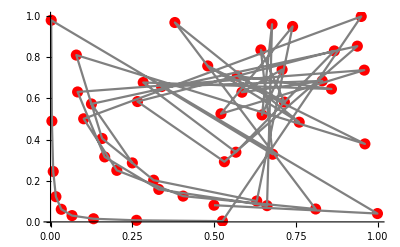

```mathematica
init=Table[{RandomReal[],RandomReal[]},1]
data=init;
p=Partition[Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data
},50]//Flatten,2];
ListPlot[p,PlotStyle->{Red,PointSize[0.02]}]~Show~ListLinePlot[p,PlotRange->{{0,1},{0,1}},PlotStyle->Gray]
```

可见其运动轨迹在单位方格内跳跃，若将上下两层染色，再进行迭代，效果如下：

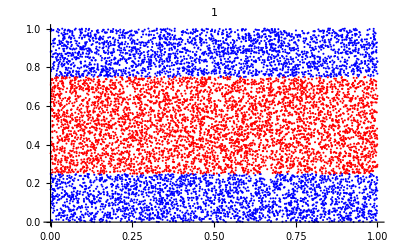
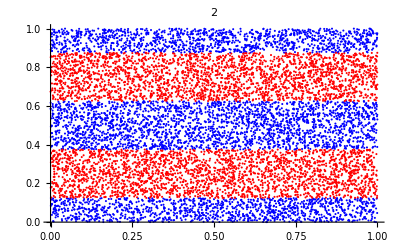
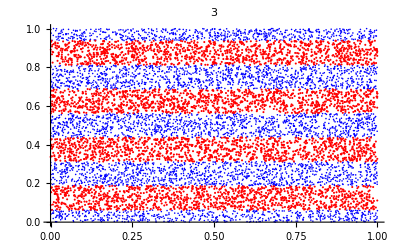
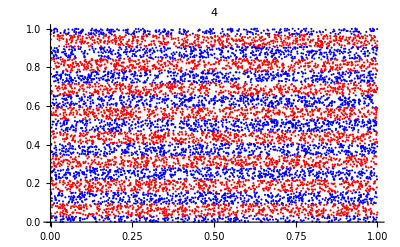
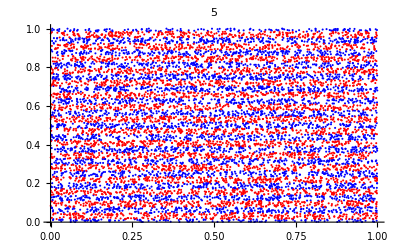

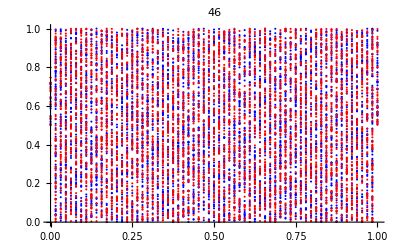
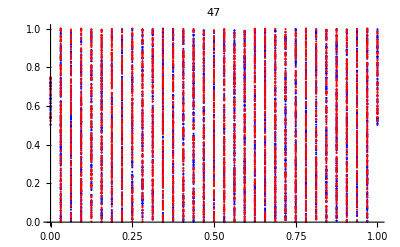
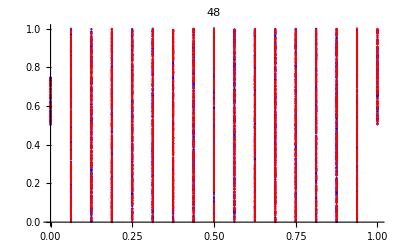

```mathematica
init=Table[{RandomReal[],0.5*RandomReal[]},5000];
init2=Table[{RandomReal[],0.5+0.5*RandomReal[]},5000];
data=init;
data2=init2;
Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data2=Table[f[data2[[i]][[1]],data2[[i]][[2]]],{i,1,Length[init]}];
ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},{0,1}},PlotLabel->iii]~Show~ListPlot[data2,PlotStyle->Red,PlotRange->{{0,1},{0,1}}]
},{iii,1,5,1}]
Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data2=Table[f[data2[[i]][[1]],data2[[i]][[2]]],{i,1,Length[init]}];
},{iii,6,45,1}];
Table[{
data=Table[f[data[[i]][[1]],data[[i]][[2]]],{i,1,Length[init]}];
data2=Table[f[data2[[i]][[1]],data2[[i]][[2]]],{i,1,Length[init]}];
ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},{0,1}},PlotLabel->iii]~Show~ListPlot[data2,PlotStyle->Red,PlotRange->{{0,1},{0,1}}]
},{iii,46,50,1}]
```

可见，刚开始时，两种颜色的点像揉面团一样相互混合。之后，当迭代次数达到46左右，开始出现纵向的分层，之后所有的点都逐渐聚集，从而出现上述图景。

logitstic map

其迭代式为：
-Graphics-
可变参数为λ,故可以以λ为横坐标，收敛得到的x为纵坐标绘制如下的分岔图：
其中初始值设为0.2

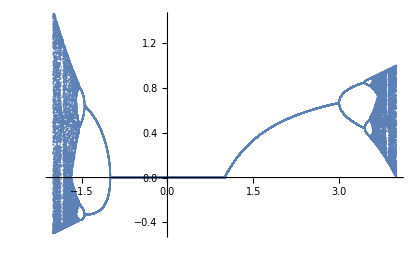

```mathematica
a=-2;b=4;c=0.001;
λ=Table[i,{i,a,b,c}];z0=Table[0.2,{i,a,b,c}];
f[x_]:=1.λ*x(1-x)
z=f[z0];
Table[z=f[z],1000];
Show[Table[{z=f[z];ListPlot[Transpose[{λ,z}]]},20]]
```

之所以λ的边界取-2和4，是因为小于-2或大于4之后，x不收敛。

Kiecked rotor model

该模型的哈密顿量为：
-Graphics-
其中，广义坐标q为角度，取值范围为0到2Pi; p为角动量。将之代入正则方程，再对一个周期进行积分，可以得到如下的迭代方程：
-Graphics-
由此可以编程进行迭代，其中设相空间中的初始点为{1,0.2}，从而迭代不同k下，相点运动的轨迹：

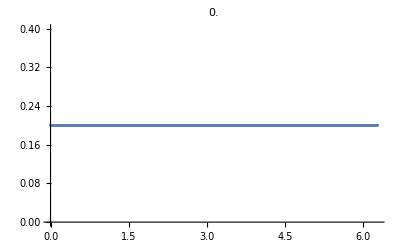
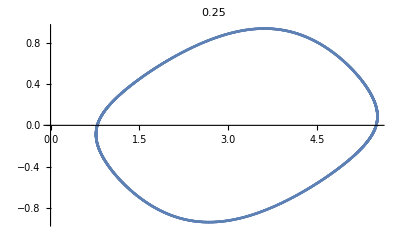
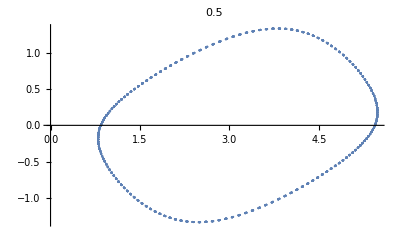
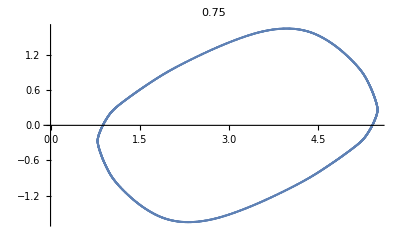
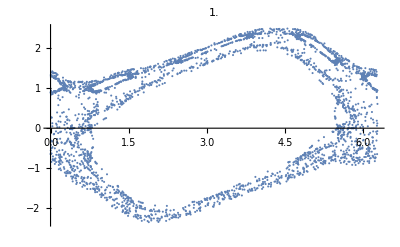
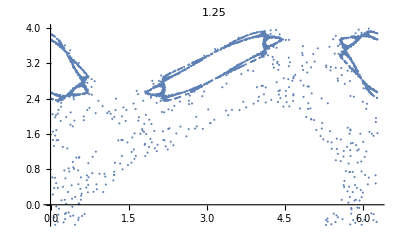
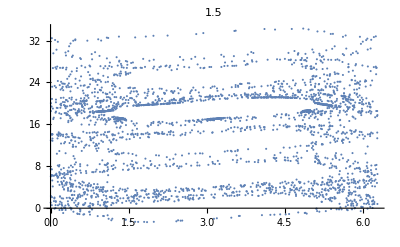
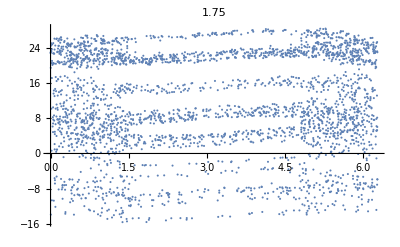

```mathematica
Table[{coor={1,0.2};
data=Table[{pnext=1.coor[[2]]+k*Sin[coor[[1]]];
qnext=Mod[coor[[1]]+pnext,2Pi];
coor={qnext,pnext};qnext,pnext},3000];
ListPlot[data,PlotLabel->k]},{k,0,4,0.25}]
```

不难发现，刚开始，相点的轨迹局限在一个环上，之后开始环破裂，分类出多种小环；随着k的增大，相点的轨迹逐渐开始扩大范围，并形成不同的圈状图案，具有混沌的性质。当k达到3之后，相点的轨迹几乎铺满的相空间。